# Hands-On Start to Mathematica

## Entering calculations

### Free-Form Input

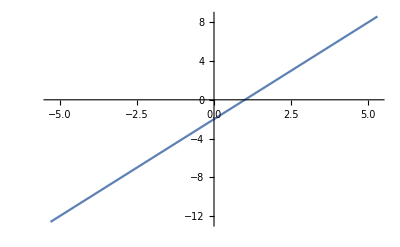

```mathematica
Plot[2*x - 2, {x, -5.3, 5.3}]
```

WolframAlphaQueryParseResults

1/2 Sin[2 x]

```mathematica
Simplify[1/2 Sin[2 x]]
```

Cos[x] Sin[x]

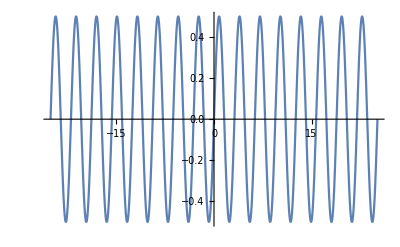

```mathematica
Plot[Cos[x] Sin[x],{x,-8 π,8 π}]
```

WolframAlphaQueryParseResults

3.18×10^6

WolframAlphaQueryParseResults

239216. $

### Wolfram Language

Capital letters to start all function names

Function arguments are enclosed by square brackets []

Lists, ranges and domains are enclosed by curly braces {}

Shift + Enter to run the calculation

```mathematica
Integrate[x^2,{x,-10,10}]
```

2000/3

### Pallets

```mathematica
Plot3D[Sin[x * y],{x,-Pi,Pi},{y,-Pi,Pi}]
```

-Graphics3D-

## Basic Calculations

```mathematica
16/728
```

2/91

```mathematica
N[2/91]
```

0.021978

```mathematica
a =5
```

5

```mathematica
3a+1
```

16

```mathematica
Clear[a]
```

```mathematica
Solve[3y + 12 == 0]
```

{{y→-4}}

```mathematica
f[x_]:= x^2
```

```mathematica
f[2]
```

4

```mathematica
g[x_, y_]:=x^y
```

```mathematica
g[10,10]
```

10000000000

```mathematica
Solve[f[x]== 36, x]
```

{{x→-6},{x→6}}

## Basic Graphics

WolframAlphaQueryParseResults

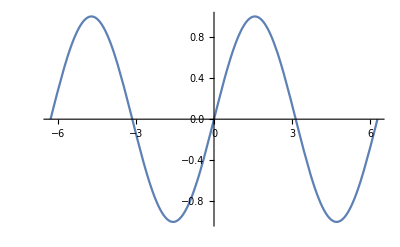

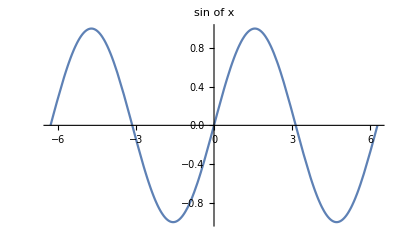

```mathematica
Show[%22,PlotLabel->HoldForm[sin of x],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Plot3D[Sin[x^2 + y^2], {x, -3, 3}, {y, -3, 3} ]
```

-Graphics3D-

```mathematica
ContourPlot[Sin[x^2 + y^2], {x, -3, 3}, {y, -3, 3} ]
```

## Interactive Models



```mathematica
Plot[Sin[x], {x, 0, 2Pi}]
```

```mathematica
Manipulate[Plot[Sin[frequency * x ], {x, 0, 2Pi}], {frequency, 1, 5}, {function, {Sin, Cos, Tan}}]
```

```mathematica
Manipulate[Expand[(y + z)^ n], {n, 2, 100, 1}]
```

## Working with Data

```mathematica
data1 = Import["http://www.handsonstart.com/ExampleDataScores.txt",{"Data"}]
```

{{Joe,Smith,94},{Jane,Smith,85},{Bob,Example,82},{Bill,Student,83},{Michelle,Abacus,98}}

```mathematica
Part[data1, 1]
```

{Joe,Smith,94}

```mathematica
data1[[1]]
```

{Joe,Smith,94}

```mathematica
data1⟦1,3⟧
```

94

```mathematica
data1[[All, 3]]
```

{94,85,82,83,98}

```mathematica
N[Mean[%]]
```

88.4

```mathematica
data2 = Import["ExampleData/50States.txt","Data"]
```

{Alabama,Alaska,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Hawaii,Idaho,Illinois,Indiana,Iowa,Kansas,Kentucky,Louisiana,Maine,Maryland,Massachusetts,Michigan,Minnesota,Mississippi,Missouri,Montana,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oklahoma,Oregon,Pennsylvania,Rhode Island,South Carolina,South Dakota,Tennessee,Texas,Utah,Vermont,Virginia,Washington,West Virginia,Wisconsin,Wyoming}

```mathematica
First[data2]
```

Alabama

```mathematica
data3 = SemanticImport["ExampleData/50States.txt"]
```

```mathematica
First[data3]
```

Alabama, United States